```mathematica
pivot[iStar_,jStar_,m_]:=(
mm=m;
numRows=Dimensions[m][[1]];
numCols=Dimensions[m][[2]];
(* switch row vars *)
mm[[1,jStar]]=m[[iStar,numCols]];
mm[[iStar,numCols]]=m[[1,jStar]];
(* switch col vars *)
mm[[numRows,jStar]]=-m[[iStar,1]];
mm[[iStar,1]]=-m[[numRows,jStar]];
(* Changed counter vars i and j to ii and jj to allow i and j to be used as tableau names *)
For[ii=2,ii<numRows,ii++,
For[jj=2,jj<numCols,jj++,
{
If[ii==iStar&&jj==jStar,mm[[ii,jj]]=1/m[[iStar,jStar]]],(* p -> 1/p *)
If[ii==iStar&&jj≠jStar,mm[[ii,jj]]=-m[[ii,jj]]/m[[iStar,jStar]]],(* q -> -q/p *)
If[ii≠iStar&&jj==jStar,mm[[ii,jj]]=m[[ii,jj]]/m[[iStar,jStar]]],(* r -> r/p *)
If[ii≠iStar&&jj≠jStar,mm[[ii,jj]]=m[[ii,jj]]-m[[iStar,jj]]*m[[ii,jStar]]/m[[iStar,jStar]]](* s -> s-qr/p *)
}
]
];
Return[mm]
)
```

```mathematica
(* graphics code not yet updated for the new LP *)
```

```mathematica
g1[x1_,x2_]=2x1+5x2; b1=80;delg1={2,5};
g2[x_,y_]=4x1+3x2; b2=76;delg2={4,3};
g3[x_,y_]=5x1+1x2; b3=84;delg3={5,1};
z[x_,y_]=16x1+19x2-10;delz={16,19};

g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
```

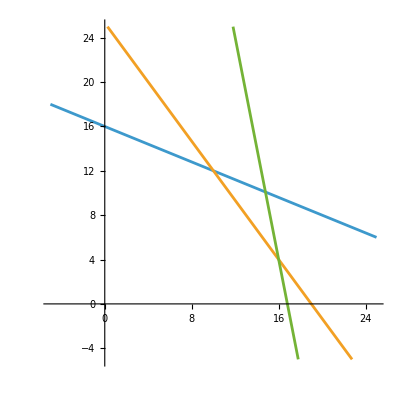

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-5,25},AspectRatio->Automatic,PlotRange->{-5,25},PlotHighlighting->None]
```

```mathematica
(* minimize z *)
db1=0;
db2=0;
db3=0;
m0={"","y1","y2","y3",1,""};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"};
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w"};
mLast={"",-"s1",-"s2",-"s3",-"z",""};
a={m0,m1,m2, mobj,mLast};
Print["db = (",db1,", ",db2,", ",db3,") Ini tab:",MatrixForm[a]]
b=pivot[2,2,a];
(* Print["b = ",MatrixForm[b]]*)
c=pivot[3,3,b];
Print["db = (",db1,", ",db2,", ",db3,") Opt tab:",MatrixForm[c]]
```

db = (0, 0, 0) Ini tab:( | y1 | y2 | y3 | 1 | 
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
-1 | 80 | 76 | 84 | -10 | w
 | -s1 | -s2 | -s3 | -z | )

db = (0, 0, 0) Opt tab:( | v1 | v2 | y3 | 1 | 
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
-1 | 10 | 12 | 22 | 378 | w
 | -x1 | -x2 | -s3 | -z | )

```mathematica
y1=2;y2=3;y3=0;v1=0;v2=0;wStar=378;
x1Base=10;x2Base=12;s3=22;zStarBase=378;
```

```mathematica
(* minimize z with non-negativity constraint for y.*)
db1=5;
db2=4;
db3=0;
m0={"","y1","y2","y3",1,""};
m1={"x1",2,4,5,-16,"v1"};
m2={"x2",5,3,1,-19,"v2"};
m3={"x3",0,0,1,0,"v3"};
mobj={-1,b1+db1,b2+db2,b3+db3,-10,"w"};
mLast={"",-"s1",-"s2",-"s3",-"z",""};
aext={m0,m1,m2,m3,mobj,mLast};
Print["db = (",db1,", ",db2,", ",db3,") Ini tab:",MatrixForm[aext]]
```

db = (5, 4, 0) Ini tab:( | y1 | y2 | y3 | 1 | 
x1 | 2 | 4 | 5 | -16 | v1
x2 | 5 | 3 | 1 | -19 | v2
x3 | 0 | 0 | 1 | 0 | v3
-1 | 85 | 80 | 84 | -10 | w
 | -s1 | -s2 | -s3 | -z | )

```mathematica
bext=pivot[2,2,aext];
(* Print["b = ",MatrixForm[b=bext]]*)
cext=pivot[3,3,bext];
Print["db = (",db1,", ",db2,", ",db3,") Opt tab:",MatrixForm[cext]]
```

db = (5, 4, 0) Opt tab:( | v1 | v2 | y3 | 1 | 
s1 | -3/14 | 2/7 | 11/14 | 2 | y1
s2 | 5/14 | -1/7 | -23/14 | 3 | y2
x3 | 0 | 0 | 1 | 0 | v3
-1 | 145/14 | 90/7 | 271/14 | 400 | w
 | -x1 | -x2 | -s3 | -z | )

```mathematica
(*get rid of the level set in x3 constrained tableuax.*)
(*we can see x3 is 22.*)
dext=pivot[, cext]
Print["db = (",db1,", ",db2,", ",db3,") Opt tab:",MatrixForm[dext]]
```

{{,v1,v2,y2,1,},{s1,-1/23,5/23,-11/23,79/23,y1},{s3,5/23,-2/23,-14/23,42/23,y3},{x3,5/23,-2/23,-14/23,42/23,v3},{-1,335/23,257/23,-271/23,10013/23,w},{,-x1,-x2,-s2,-z,}}

db = (5, 4, 0) Opt tab:( | v1 | v2 | y2 | 1 | 
s1 | -1/23 | 5/23 | -11/23 | 79/23 | y1
s3 | 5/23 | -2/23 | -14/23 | 42/23 | y3
x3 | 5/23 | -2/23 | -14/23 | 42/23 | v3
-1 | 335/23 | 257/23 | -271/23 | 10013/23 | w
 | -x1 | -x2 | -s2 | -z | )